```mathematica
x[t_]=Exp[t/4]*Sin[2Pi*t/4];
```

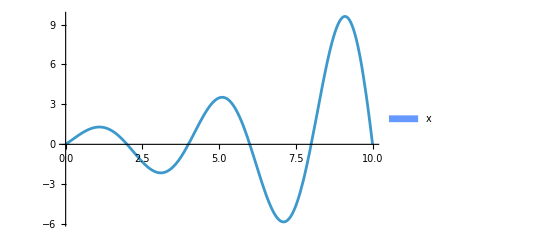

```mathematica
plt x=Plot[x[t],{t,0,10},PlotLegends->SwatchLegend[{StandardBlue}, {"x"}]]
```

```mathematica
L1=11;
```

```mathematica
t arr={0,1.5,2.1,3,3.8,5,5.7,6.7,8,9.1,10};
```

```mathematica
M1=11;T tld=1;
```

```mathematica
t tld arr=Table[i*T tld,{i,0,M1-1}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
x arr=Table[N[x[t arr[[i]]]],{i,L1}]
```

{0.,1.02883,-0.264446,-2.117,-0.799028,3.49034,1.88763,-4.7569,0.,9.60815,0.}

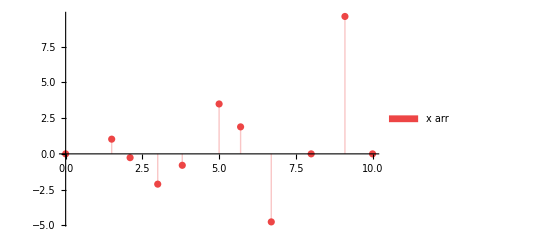

```mathematica
plt x arr=ListPlot[Transpose[{t arr,x arr}],Filling->Axis,PlotStyle->StandardRed,PlotLegends->SwatchLegend[{StandardRed}, {"x arr"}]]
```

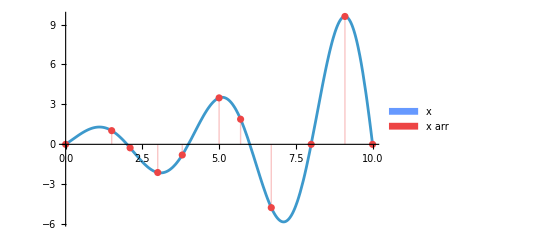

```mathematica
Show[plt x,plt x arr]
```

```mathematica
a[l_,m_]:=Sinc[Pi*(t arr[[1+l]]-m*T tld)/T tld]
```

```mathematica
A=Table[N[a[l,m]],{l,0,L1-1},{m,0,M1-1}];A//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.212207 | 0.63662 | 0.63662 | -0.212207 | 0.127324 | -0.0909457 | 0.0707355 | -0.0578745 | 0.0489708 | -0.0424413 | 0.0374482
0.0468396 | -0.0894211 | 0.983632 | 0.109292 | -0.0517701 | 0.0339183 | -0.0252213 | 0.0200741 | -0.0166717 | 0.0142555 | -0.012451
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0492363 | 0.0668207 | -0.103943 | 0.233872 | 0.935489 | -0.155915 | 0.0850445 | -0.0584681 | 0.0445471 | -0.0359804 | 0.0301771
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
-0.0451786 | 0.0547911 | -0.0695995 | 0.0953771 | -0.151481 | 0.367883 | 0.858394 | -0.198091 | 0.111964 | -0.0780358 | 0.0598879
0.0384355 | -0.0451786 | 0.0547911 | -0.0695995 | 0.0953771 | -0.151481 | 0.367883 | 0.858394 | -0.198091 | 0.111964 | -0.0780358
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
-0.0108091 | 0.0121436 | -0.013854 | 0.0161251 | -0.0192869 | 0.023991 | -0.0317301 | 0.0468396 | -0.0894211 | 0.983632 | 0.109292
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
MatrixRank[A]==L1
```

True

```mathematica
(*x tld arr=Transpose[A].Inverse[A.Transpose[A]].x arr*)
x tld arr=Inverse[A].x arr
```

{0.,1.45903,-0.0218905,-2.117,0.106157,3.49034,0.282474,-6.45871,0.,10.018,0.}

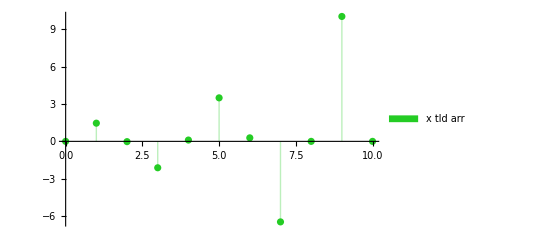

```mathematica
plt x tld arr=ListPlot[Transpose[{t tld arr,x tld arr}],PlotRange->Full,Filling->Axis,PlotStyle->StandardGreen,PlotLegends->SwatchLegend[{StandardGreen}, {"x tld arr"}]]
```

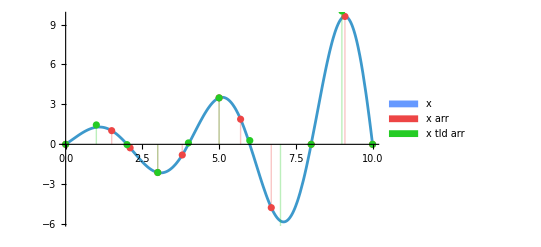

```mathematica
Show[plt x,plt x arr,plt x tld arr]
```

```mathematica
x tld[t_]:=Sum[Sinc[Pi*(t-m*T tld)/T tld]*x tld arr[[1+m]],{m,0,M1-1}]
```

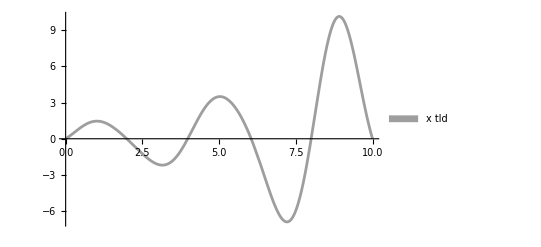

```mathematica
plt x tld=Plot[x tld[t],{t,0,10},PlotStyle->StandardGray,PlotLegends->SwatchLegend[{StandardGray}, {"x tld"}]]
```

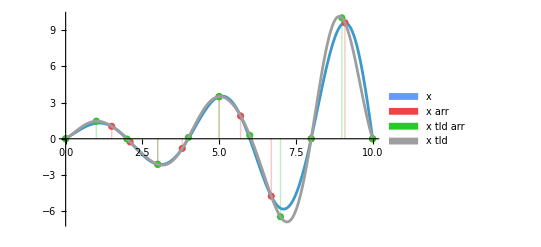

```mathematica
plt all=Show[plt x,plt x arr,plt x tld arr,plt x tld,PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[]<>"/plot.pdf",plt all]
```

## Compare with spline interpolation

```mathematica
x spline=Interpolation[Transpose[{t arr,x arr}],Method->"Spline"]
```

InterpolatingFunction[…]

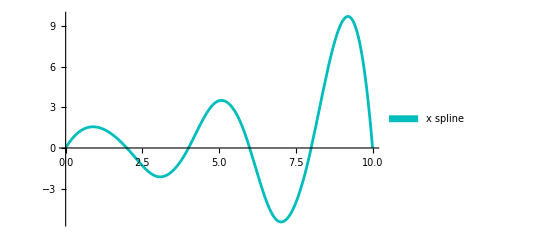

```mathematica
plt x sp=Plot[x spline[t],{t,0,L1-1},PlotStyle->StandardCyan,PlotLegends->SwatchLegend[{StandardCyan}, {"x spline"}]]
```

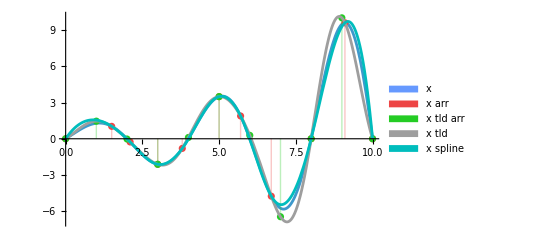

```mathematica
plt all2=Show[plt x,plt x arr,plt x tld arr,plt x tld,plt x sp,PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[]<>"/plot.pdf",plt all2]
```

C:\Users\motchy\Desktop\/plot.pdf